Nacho’s solution and parameters

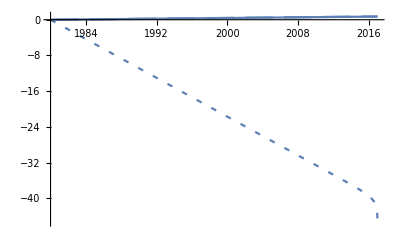

-0.0286415

```mathematica
ωx = 0.65;ωc = 0.29;
θ=0.333;ρ=0.04;δ=0.08;η=0.271755246774759;χ=0.55;γ=0.99;

E0=1.19126274003461;K0=3.99345071351064;ν0=0.998041621691275;Y0=1.58653421667796;

gpg=Log[1.068]/37;
gps=Log[1.575]/37;
gK=(Log[7.802]-Log[3.865])/37;
gnu=(Log[0.526]-Log[0.926])/37;

Pg[t_]=ⅇ^(gpg(t-1980));
Ps[t_]=ⅇ^(gps(t-1980));
EE[t_]=E0 ⅇ^(gK(t-1980));
K[t_]=K0 ⅇ^(gK(t-1980));
Y[t_]=Y0 ⅇ^(gK(t-1980));
ν[t_]=ν0 ⅇ^(gnu(t-1980));
M[t_]=Y[t]-δ K[t];

V[exp_,pg_,ps_]=1/χ(exp/ps)^χ-η/γ(pg/ps)^γ-1/χ+η/γ;

indu[m_,pg_,ps_,nu_]=V[(nu ps^χ)^(1/(χ-1)),pg,ps]+nu(m-(nu ps^χ)^(1/(χ-1)));
expf[w_,pg_,ps_,nu_]=(nu ps^χ)^(1/(χ-1))+w/nu-V[(nu ps^χ)^(1/(χ-1)),pg,ps]/nu;
Mhat[t_,z_]=expf[indu[M[z],Pg[z],Ps[z],ν[t]],Pg[t],Ps[t],ν[t]];

fig2017=Plot[Log[Mhat[2017,z]]-Log[Mhat[2017,1980]],{z,1980,2017},PlotStyle->Dashing[{0.01,0.02}]];
fig1980=Plot[Log[Mhat[1980,z]]-Log[Mhat[1980,1980]],{z,1980,2017},PlotStyle->Dashing[{0.05,0.02}]];
figM=Plot[Log[M[z]]-Log[M[1980]],{z,1980,2017}];
fig=Show[%,%%,%%%,PlotRange->All]

Log[M[2017]]-Log[Mhat[1980,2017]]
```

NDP

0.94018

0.000180116

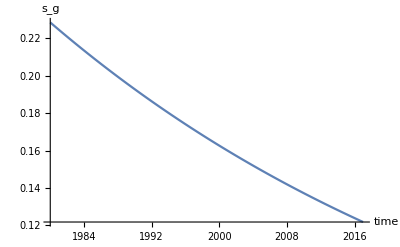

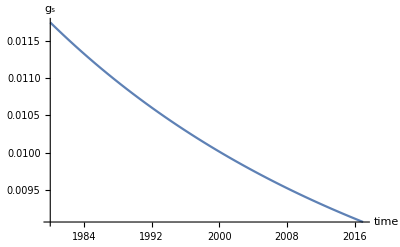

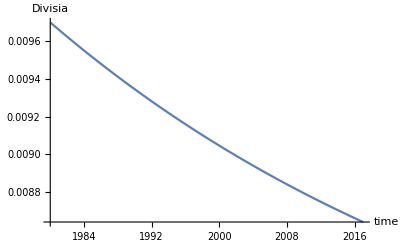

```mathematica
se=EE[1980]/M[1980]

gg=(1-χ)gK+(γ-1)gpg+(χ-γ)gps

sg[t_]=η(EE[t]/Ps[t])^-χ(Pg[t]/Ps[t])^γ;
Plot[sg[t],{t,1980,2017},AxesLabel->{"time","s_g"}]

Cs[t_]=EE[t]/Ps[t](1-sg[t]);
Plot[Cs[t],{t,1980,2017}];
gs[t_]=Simplify[D[Log[Cs[t]],t]];
Plot[gs[t],{t,1980,2017},AxesLabel->{"time","g_s"}]

Divisia[t_]=Simplify[se(sg[t]gg+(1-sg[t])gs[t])+(1-se)gK];
Plot[Divisia[t],{t,1980,2017},AxesLabel->{"time","Divisia"}]
```

```mathematica
FS=Table[{n,NIntegrate[Divisia[t],{t,1980,n}]},{n,1980,2017,0.001}];
```

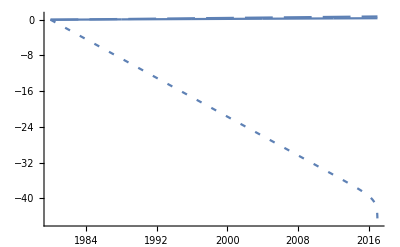

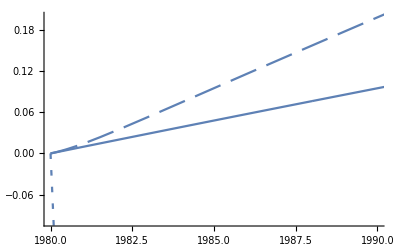

```mathematica
ListPlot[FS,Joined -> True];
Show[%,fig2017,fig1980,PlotRange->All]
Show[%%,fig2017,fig1980,PlotRange->{{1980,1990},{0-.1,.2}}]
```

GDP

0.756211

0.00627293

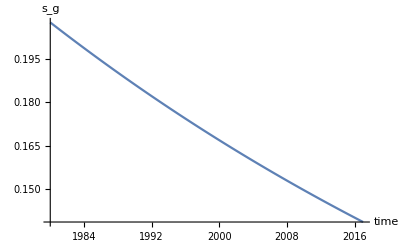

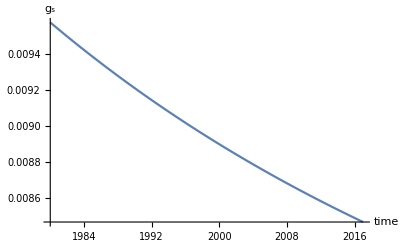

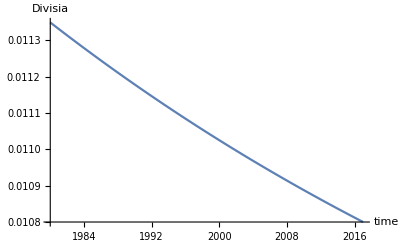

```mathematica
se=EE[1980]/Y[1980]

gg=(1-χ)gK+(γ-1)gpg+(χ-γ)gps

sg[t_]=η(EE[t]/Ps[t])^-χ(Pg[t]/Ps[t])^γ;
Plot[sg[t],{t,1980,2017},AxesLabel->{"time","s_g"}]

Cs[t_]=EE[t]/Ps[t](1-sg[t]);
Plot[Cs[t],{t,1980,2017}];
gs[t_]=Simplify[D[Log[Cs[t]],t]];
Plot[gs[t],{t,1980,2017},AxesLabel->{"time","g_s"}]

Divisia[t_]=Simplify[se(sg[t]gg+(1-sg[t])gs[t])+(1-se)gK];
Plot[Divisia[t],{t,1980,2017},AxesLabel->{"time","Divisia"}]
```

```mathematica
FS=Table[{n,NIntegrate[Divisia[t],{t,1980,n}]},{n,1980,2017,0.001}];
```

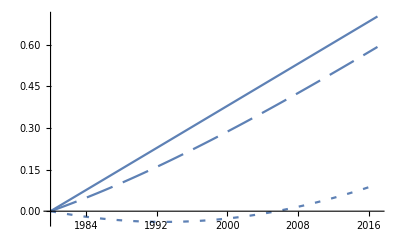

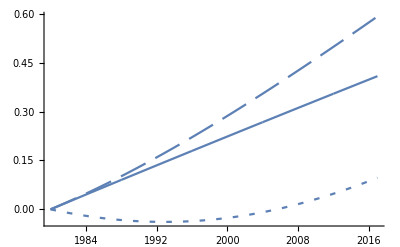

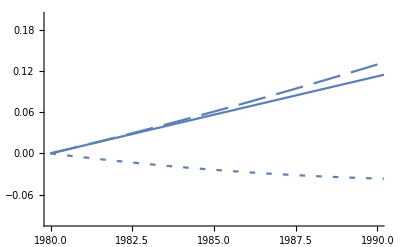

```mathematica
Mhat[t_,z_]=expf[indu[Y[z],Pg[z],Ps[z],ν[t]],Pg[t],Ps[t],ν[t]];

fig2017=Plot[Log[Mhat[2017,z]]-Log[Mhat[2017,1980]],{z,1980,2017},PlotStyle->Dashing[{0.01,0.02}]];
fig1980=Plot[Log[Mhat[1980,z]]-Log[Mhat[1980,1980]],{z,1980,2017},PlotStyle->Dashing[{0.05,0.02}]];
figM=Plot[Log[Y[z]]-Log[Y[1980]],{z,1980,2017}];
fig=Show[%,%%,%%%,PlotRange->All]

ListPlot[FS,Joined -> True];
Show[%,fig2017,fig1980,PlotRange->All]
Show[%%,fig2017,fig1980,PlotRange->{{1980,1990},{0-.1,.2}}]
```